can I do efficient cooling by PGC in a shallow trap to n = ni, then ramping diabatically to a deep trap? Is the overlap between the initial ni in shallow trap and n=0 in the deep trap any good?

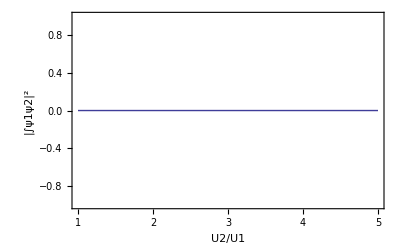

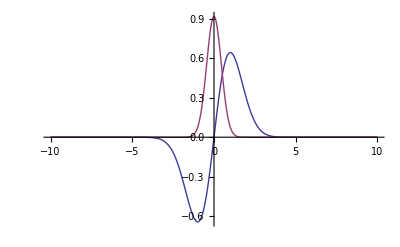

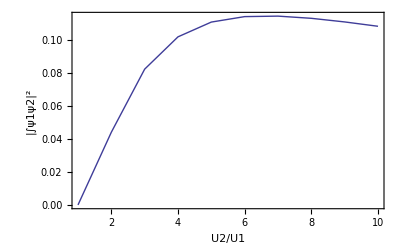

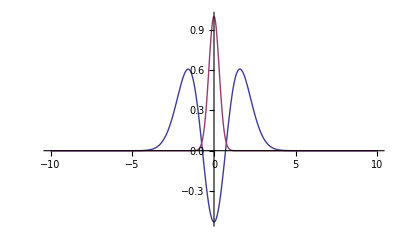

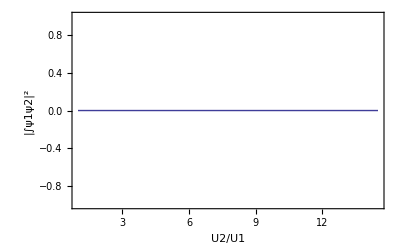

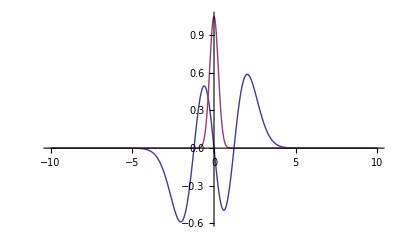

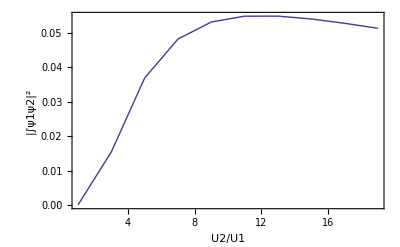

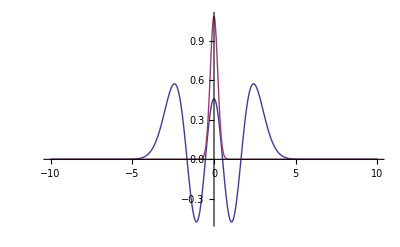

```mathematica
maxoverlaps=Reap[
Do[Umax=5ni;
overlap=Reap[
Do[
m=1;
ℏ=1;

sub1=ω->1;
sub2=ω->√U2;

α=(m ω)/ℏ;
y=α x;
ψ=(α/π)^(1/4)1/(√(2^n n!))HermiteH[n,y]Exp[-y^2/2.];

(*start in ni*)
f1=ψ/.sub1/.n->ni;
(*end in gnd state*)
f2=ψ/.sub2/.n->0;


If[EvenQ[ni],
data=Abs[Integrate[f1 f2,{x,-Infinity, Infinity}]]^2,
data=0];

Sow[{U2,data}]

,{U2,1,Umax,Umax/10}]
][[2,1]];

Print[ListPlot[overlap,Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"U2/U1","|∫ψ1ψ2|^2","ni="<>ToString[ni]},PlotRange->All]
];

Print[
Plot[{f1,f2},{x,-10,10},PlotRange->All]
];
posMax=1. overlap[[Flatten[Position[overlap[[;;,2]],Max[overlap[[;;,2]]]]][[1]]]][[1]];
(*position of largest overlap*)
Sow[{ni,Max[overlap[[;;,2]]],posMax}];
,{ni,1,10}]
][[2,1]];
```

## as a function of starting ni in the shallow trap: 1)what’s the maximum overlap with the ground state in the deep trap, and 2)how high do I have to ramp up trap depth to get the best overlap

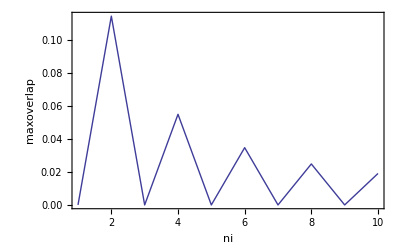

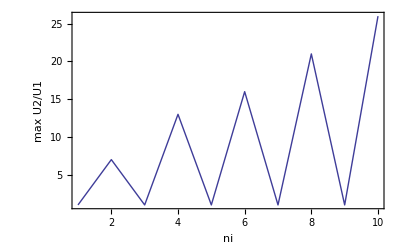

```mathematica
ListPlot[maxoverlaps[[;;,{1,2}]],Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"ni","maxoverlap"}]

ListPlot[maxoverlaps[[;;,{1,3}]],Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"ni","max U2/U1"}]
```

conclusion: 

first of all, there is no overlap between odd ni and n=0. For even ni, as you get to larger ni, the trap depth required to get optimal overlap with the ground state increases--> bad b/c limited power.
second, even for small initial ni, the overlap is ~10%. So this is not very efficient at all.
third, it’s probably worse in 3d. And I don’t know if you can satisfy simultaneously for radial and axial dimensions. 
so forget it.